```mathematica
Clear[t,x,h]
n=1000;
m=20;
b[t_]:=1/m;
k[t_]:=100/m;
f[t_]:=4*Sin[2*t]/m;
t[0]=0;
t[n]=100;
h=(t[n]-t[0])/n;
t[i_]:=t[0]+h*i;
x[0]=0;
x[n]=0;
```

```mathematica
EQN=Table[(1+(h/2)*b[t[i]])*x[i+1]+(-2+h^2*k[t[i]])*x[i]+(1-(h/2)*b[t[i]])*x[i-1]==h^2*f[t[i]],{i,n-1}];
```

```mathematica
Solutions=NSolve[EQN];
```

```mathematica
txlist={{t[0],x[0]}};
```

```mathematica
For[i=1,i<n,i++,x[i]=x[i]/.Solutions[[1]];
txlist=Append[txlist,{t[i],x[i]}];]
```

```mathematica
txlist=Append[txlist,{t[n],x[n]}];
```

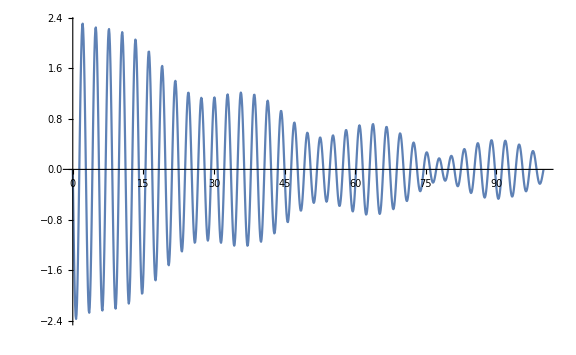

```mathematica
txgraph=ListPlot[txlist,Joined-> True,ImageSize-> Large]
```